```mathematica
yints[m_,ν_,h_,n_,λ_] = 1/4 Sqrt[2/π](Integrate[I(π/h)^(1+m)(x+I y)^m Exp[- λ π/h(x+I y)]Exp[-I(π/h(x+I y)- ν π/2- π/4)],{y,-z,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0}]+Integrate[-I(π/h)^(1+m)(x+I y)^m Exp[- λ π/h(x+I y)]Exp[I(π/h(x+I y)- ν π/2- π/4)],{y,0,z}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0}]-Integrate[-I(π/h)^(1+m)(x+I y)^m Exp[- λ π/h(x+I y)]Exp[I(π/h(x+I y)- ν π/2- π/4)],{y,z,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0}]-Integrate[I(π/h)^(1+m)(x+I y)^m Exp[- λ π/h(x+I y)]Exp[-I(π/h(x+I y)- ν π/2- π/4)],{y,0,-z}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0}])/.x-> h(n+ν/2+1/4)/.z-> π/2;
```

```mathematica
ogerror[μ_,ν_,h_,n_,λ_] = Simplify[yints[μ-1/2,ν,h,n,λ], Assumptions->{h>0,n>0,λ>0,ν>0}];
```

```mathematica
Exact[μ_,ν_,λ_] = Integrate[(π/h)^(μ+1)x^μ Exp[- (λ π x)/h]BesselJ[ν,π/h x], {x,0,Infinity}, Assumptions->{ν>0,λ>0,h>0,μ>0}];
```

```mathematica
cutoff[m_,ν_,h_,n_,λ_] = Integrate[(π/h)^(μ+1/2)Sqrt[π/2] x^(μ-1/2) Exp[- (λ π x)/h]Cos[π/h x- ν/2-1/4], {x,h(n+ν/2+1/4),Infinity},Assumptions->{ν>0,λ>0,h>0,R>0,n>0,μ>0}];
```

```mathematica
OgerrorRat[μ_,ν_,h_,n_,λ_] = ogerror[μ,ν,h,n,λ]/Exact[μ,ν,h,λ];
cutRat[μ_,ν_,h_,n_,λ_] = cutoff[m,ν,h,n,λ]/Exact[μ,ν,h,λ];
```

```mathematica
Abs[ogerror[1,0,0.1,10,0.1]/Exact[1,0,0.1,0.1]]
```

0.154262

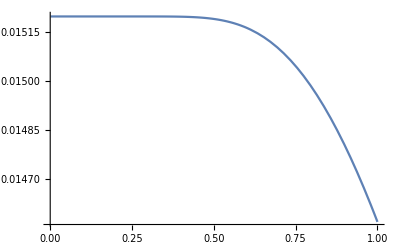

```mathematica
Plot[Abs[ogerror[1,0,h,10,0.1] ],{h,0.001,1}, PlotRange->All]
```

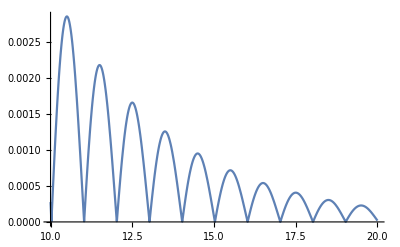

```mathematica
Plot[Abs[cutoff/Exact]/.λ-> 0.1/.x-> h (n+ν/2+1/4)/.n-> 20/.z-> π/2/.ν-> 0/.h-> 0.1,{n,10,20}, PlotRange->All]
```

```mathematica
Integrate[(β^α x^(α-1)E^(- β x))/Gamma[α] x^2,{x,0,Infinity}, Assumptions->{α>0,β>0}]-(Integrate[(β^α x^(α-1)E^(- β x))/Gamma[α] x,{x,0,Infinity}, Assumptions->{α>0,β>0}])^2
```

-α^2/β^2+(α (1+α))/β^2

```mathematica
Simplify[%30, Assumptions->{β>0,α>0}]
```

α/β^2

```mathematica
Solve[D[(β^α x^(α-1)E^(- β x))/Gamma[α],x] == 0,x]
```

{{x→(-1+α)/β}}

```mathematica
Simplify[Solve[{1/Q ==(-1+α)/β, σ^2 == α/β^2}, {α,β} ], Assumptions->{Q>0,σ>0}]
```

{{α→(1+2 Q^2 σ^2-√(1+4 Q^2 σ^2))/(2 Q^2 σ^2),β→-(-1+√(1+4 Q^2 σ^2))/(2 Q σ^2)},{α→(1+2 Q^2 σ^2+√(1+4 Q^2 σ^2))/(2 Q^2 σ^2),β→(1+√(1+4 Q^2 σ^2))/(2 Q σ^2)}}

```mathematica
((1+2 Q^2 σ^2+√(1+4 Q^2 σ^2))/(2 Q^2 σ^2))/.σ-> 2.5/.Q-> 1
((1+√(1+4 Q^2 σ^2))/(2 Q σ^2))/.σ-> 2.5/.Q-> 1
```

```mathematica
(β^α x^(α-1)E^(- β x))/Gamma[α]/.α-> %50/.β-> %51
```

0.388066 ⅇ^(-0.487922 x) x^0.487922

```mathematica
0.487921561087423-0.5
```

-0.0120784

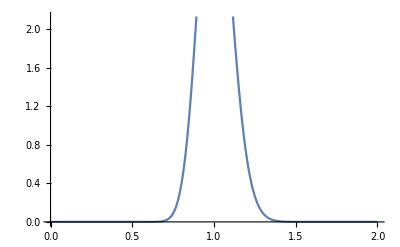

```mathematica
Plot[%37/.σ-> 0.1/.Q-> 1, {x,0,2}]
```

```mathematica
Integrate[(I(π/h)(π/h)^(1/2-12/1000)(x+I y)^(-12/1000)Exp[- λ π/h(x+I y)]Exp[-I(π/h(x+I y)- ν π/2- π/4)])/.ν-> 0,{y,-z,0}, Assumptions->{h>0,λ>0,z>0,x>0, m≥ 0,σ>0, m≥ 0, Element[m,Integers]}]
```

-((1+ⅈ) π^(186/125) (x^(247/250) ExpIntegralE[3/250,(π x (ⅈ+λ))/h]-(x-ⅈ z)^(247/250) ExpIntegralE[3/250,(π (x-ⅈ z) (ⅈ+λ))/h]))/(√2 h^(186/125))

```mathematica
Plot[%27/.z-> ]
```

```mathematica
I(π/h)^(3/2)0.388066372573678Integrate[(x+I y)^(-12/1000) ⅇ^(-π/h λ (x+I y))Exp[-I(π/h(x+I y)- π/4)],{y,-z,0}, Assumptions->{h>0,λ>0,z>0,x>0, m≥ 0,σ>0, m>1/2}]
```

(-1.52797-1.52797 ⅈ) (1/h)^(3/2) (x^(247/250) ExpIntegralE[3/250,(π x (ⅈ+λ))/h]-(x-ⅈ z)^(247/250) ExpIntegralE[3/250,(π (x-ⅈ z) (ⅈ+λ))/h])

```mathematica
Abs[%61/.x-> h(4+1/4)/.h-> 8.6*10^-7/.z-> π/2/.λ-> 0.4879215610874228]
```

1.1473

```mathematica
Abs[%61/.x-> h(9+1/4)/.h-> 1.08*10^-7/.z-> π/2/.λ-> 0.4879215610874228]
```

0.00154356

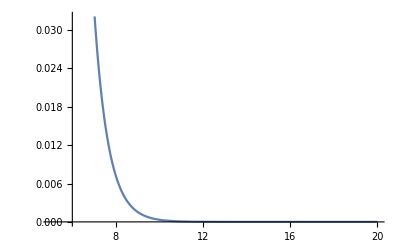

```mathematica
Plot[Abs[%61]/.x-> h(n+1/4)/.h-> 1.08*10^-7/.z-> π/2/.λ-> 0.4879215610874228,{n,5,20}]
```

```mathematica
Integrate[I(π/h)^(3/2)(x+I y)^(1/2)Exp[- λ π/h(x+I y)^2]Exp[-I(π/h(x+I y)- ν π/2- π/4)],{y,-z,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0, m≥ 0,σ>0}]
```

Integrate[ⅈ ⅇ^(-(π (x+ⅈ y)^2 λ)/h-ⅈ (-π/4+(π (x+ⅈ y))/h-(π ν)/2)) (1/h)^(3/2) π^(3/2) √(x+ⅈ y),{y,-z,0},Assumptions→{ν>0,h>0,λ>0,z>0,x>0,m≥0,σ>0}]

```mathematica
Exp[- λ x^2-I x+(ⅈ+2 x λ)^2/(4 λ)]Integrate[(x+I y)^(1/2)Exp[(-ⅈ x+y+1/(2 λ))^2 λ],{y,-z,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0, m≥ 0,σ>0}]
```

ⅇ^(-ⅈ x-x^2 λ+(ⅈ+2 x λ)^2/(4 λ)) Integrate[ⅇ^((-ⅈ x+y+1/(2 λ))^2 λ) √(x+ⅈ y),{y,-z,0},Assumptions→{ν>0,h>0,λ>0,z>0,x>0,m≥0,σ>0}]

```mathematica
Integrate[I(π/h)^(m+3/2)(x+I y)^(m+1/2)Exp[- λ π/h(x+I y)^2]Exp[-I(π/h(x+I y)- π/4)],{y,-π/2,0}, Assumptions->{ν>0,h>0,λ>0,z>0,x>0, m≥ 0,σ>0}]
```

Integrate[ⅈ ⅇ^(-ⅈ (-π/4+(π (x+ⅈ y))/h)-(π (x+ⅈ y)^2 λ)/h) (1/h)^(3/2+m) π^(3/2+m) (x+ⅈ y)^(1/2+m),{y,-π/2,0},Assumptions→{ν>0,h>0,λ>0,z>0,x>0,m≥0,σ>0}]

```mathematica
Q = 1/(x/.Solve[D[x^n Exp[- λ x],x] == 0, x][[1]])
σ2 = Simplify[Integrate[x^(n+2)Exp[- λ x],{x,0,Infinity}, Assumptions->{n≥ 0, λ>0}]-( Integrate[x^(n+1)Exp[- λ x],{x,0,Infinity}, Assumptions->{n≥ 0, λ>0}])^2, Assumptions->{n≥ 0, λ>0}]
```

λ/n

λ^(-2 (2+n)) (-Gamma[2+n]^2+λ^(1+n) Gamma[3+n])

```mathematica
Simplify[((-1)^(3/4) 4^(-1-m) ⅇ^(-1/2 ⅈ π ν) ((π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)])-(-1)^(3/4) 4^(-1-m) ⅇ^(-1/2 ⅈ π ν) (-(π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]+π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)])-1/(ⅈ+λ)2 (-1)^(1/4) ⅇ^((ⅈ π ν)/2) h^-m (h^m (ⅈ+λ)^-m Gamma[1+m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]-(h (h+4 h n-2 ⅈ π+2 h ν))^m ((ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))^-m Gamma[1+m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]))/.ν-> 0, Assumptions->{m>0,λ>0,n>0,h>0}]
```

1/2 (-1)^(1/4) (ⅈ 4^-m (1+4 n) π (π+4 n π)^m ExpIntegralE[-m,1/4 (1+4 n) π (-ⅈ+λ)]-(ⅈ (h+4 h n+2 ⅈ π) π^(1+m) (1/4+n+(ⅈ π)/(2 h))^m ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/h+1/(ⅈ+λ)4 (-(ⅈ+λ)^-m Gamma[1+m,1/4 (1+4 n) π (ⅈ+λ)]+(h+4 h n-2 ⅈ π)^m ((h+4 h n-2 ⅈ π) (ⅈ+λ))^-m Gamma[1+m,((h+4 h n-2 ⅈ π) π (ⅈ+λ))/(4 h)]))

```mathematica
%10//Apart
```

-((-1)^(1/4) 2^(-1-2 m) π (π+4 n π)^m ExpIntegralE[-m,1/4 (1+4 n) π (-ⅈ+λ)])/(ⅈ+λ)-((-1)^(1/4) 2^(1-2 m) n π (π+4 n π)^m ExpIntegralE[-m,1/4 (1+4 n) π (-ⅈ+λ)])/(ⅈ+λ)+((-1)^(3/4) 2^(-1-2 m) π (π+4 n π)^m λ ExpIntegralE[-m,1/4 (1+4 n) π (-ⅈ+λ)])/(ⅈ+λ)+((-1)^(3/4) 2^(1-2 m) n π (π+4 n π)^m λ ExpIntegralE[-m,1/4 (1+4 n) π (-ⅈ+λ)])/(ⅈ+λ)+((-1)^(1/4) π^(1+m) (1/4+n+(ⅈ π)/(2 h))^m ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/(2 (ⅈ+λ))+(2 (-1)^(1/4) n π^(1+m) (1/4+n+(ⅈ π)/(2 h))^m ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/(ⅈ+λ)+((-1)^(3/4) π^(2+m) (1/4+n+(ⅈ π)/(2 h))^m ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/(h (ⅈ+λ))-((-1)^(3/4) π^(1+m) (1/4+n+(ⅈ π)/(2 h))^m λ ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/(2 (ⅈ+λ))-(2 (-1)^(3/4) n π^(1+m) (1/4+n+(ⅈ π)/(2 h))^m λ ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/(ⅈ+λ)+((-1)^(1/4) π^(2+m) (1/4+n+(ⅈ π)/(2 h))^m λ ExpIntegralE[-m,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)])/(h (ⅈ+λ))-2 (-1)^(1/4) (ⅈ+λ)^(-1-m) Gamma[1+m,1/4 (1+4 n) π (ⅈ+λ)]+(2 (-1)^(1/4) (h+4 h n-2 ⅈ π)^m ((h+4 h n-2 ⅈ π) (ⅈ+λ))^-m Gamma[1+m,((h+4 h n-2 ⅈ π) π (ⅈ+λ))/(4 h)])/(ⅈ+λ)

```mathematica
Simplify[%11/.m-> 1/2, Assumptions->{m>0,λ>0,n>0,h>0}]
```

((-1)^(1/4) (ⅈ h π^(3/2) ((1+4 n) (ⅈ+λ))^(3/2) √((h+4 h n-2 ⅈ π) (ⅈ+λ)) ExpIntegralE[-1/2,1/4 (1+4 n) π (-ⅈ+λ)]-ⅈ (h+4 h n+2 ⅈ π) π^(3/2) √(1+4 n+(2 ⅈ π)/h) (ⅈ+λ)^(3/2) √((h+4 h n-2 ⅈ π) (ⅈ+λ)) ExpIntegralE[-1/2,((h+4 h n+2 ⅈ π) π (-ⅈ+λ))/(4 h)]-8 h √((h+4 h n-2 ⅈ π) (ⅈ+λ)) Gamma[3/2,1/4 (1+4 n) π (ⅈ+λ)]+8 h √(h+4 h n-2 ⅈ π) √(ⅈ+λ) Gamma[3/2,((h+4 h n-2 ⅈ π) π (ⅈ+λ))/(4 h)]))/(4 h (ⅈ+λ)^(3/2) √((h+4 h n-2 ⅈ π) (ⅈ+λ)))

```mathematica
TeXForm[-(-1)^(1/4) 4^(-1-m) ⅇ^((ⅈ π ν)/2) ((π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]-π^(1+m) (1+4 n-(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)])+(-1)^(1/4) 4^(-1-m) ⅇ^((ⅈ π ν)/2) (-(π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]+π^(1+m) (1+4 n-(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)])+(-1)^(3/4) 4^(-1-m) ⅇ^(-1/2 ⅈ π ν) ((π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)])-(-1)^(3/4) 4^(-1-m) ⅇ^(-1/2 ⅈ π ν) (-(π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]+π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)])]
```

-\sqrt[4]{-1} 4^{-m-1} e^{\frac{i \pi  \nu }{2}} \left((2 \pi  \nu +4 \pi  n+\pi )^{m+1}
   E_{-m}\left(\frac{1}{4} \pi  (\lambda +i) (4 n+2 \nu +1)\right)-\pi ^{m+1} \left(-\frac{2 i \pi }{h}+2
   \nu +4 n+1\right)^{m+1} E_{-m}\left(\frac{\pi  (\lambda +i) (4 n h+2 \nu  h+h-2 i \pi )}{4
   h}\right)\right)+\sqrt[4]{-1} 4^{-m-1} e^{\frac{i \pi  \nu }{2}} \left(\pi ^{m+1} \left(-\frac{2 i \pi
   }{h}+2 \nu +4 n+1\right)^{m+1} E_{-m}\left(\frac{\pi  (\lambda +i) (4 n h+2 \nu  h+h-2 i \pi )}{4
   h}\right)-(2 \pi  \nu +4 \pi  n+\pi )^{m+1} E_{-m}\left(\frac{1}{4} \pi  (\lambda +i) (4 n+2 \nu
   +1)\right)\right)+(-1)^{3/4} 4^{-m-1} e^{-\frac{1}{2} i \pi  \nu } \left((2 \pi  \nu +4 \pi  n+\pi
   )^{m+1} E_{-m}\left(\frac{1}{4} \pi  (\lambda -i) (4 n+2 \nu +1)\right)-\pi ^{m+1} \left(\frac{2 i \pi
   }{h}+2 \nu +4 n+1\right)^{m+1} E_{-m}\left(\frac{\pi  (\lambda -i) (4 n h+2 \nu  h+h+2 i \pi )}{4
   h}\right)\right)-(-1)^{3/4} 4^{-m-1} e^{-\frac{1}{2} i \pi  \nu } \left(\pi ^{m+1} \left(\frac{2 i \pi
   }{h}+2 \nu +4 n+1\right)^{m+1} E_{-m}\left(\frac{\pi  (\lambda -i) (4 n h+2 \nu  h+h+2 i \pi )}{4
   h}\right)-(2 \pi  \nu +4 \pi  n+\pi )^{m+1} E_{-m}\left(\frac{1}{4} \pi  (\lambda -i) (4 n+2 \nu
   +1)\right)\right)

```mathematica
Simplify[-(-1)^(1/4) 4^(-1-m) ⅇ^((ⅈ π ν)/2) ((π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]-π^(1+m) (1+4 n-(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)])+(-1)^(1/4) 4^(-1-m) ⅇ^((ⅈ π ν)/2) (-(π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]+π^(1+m) (1+4 n-(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)])+(-1)^(3/4) 4^(-1-m) ⅇ^(-1/2 ⅈ π ν) ((π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)])-(-1)^(3/4) 4^(-1-m) ⅇ^(-1/2 ⅈ π ν) (-(π+4 n π+2 π ν)^(1+m) ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]+π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^(1+m) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)]), Assumptions->{h>0,n>0,m>0,ν>0}]//Apart
```

-1/h(-1)^(1/4) 2^(-1-2 m) ⅇ^(-1/2 ⅈ π ν) π (-ⅈ h (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-4 ⅈ h n (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-2 ⅈ h ν (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]+ⅇ^(ⅈ π ν) h (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]+4 ⅇ^(ⅈ π ν) h n (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]+2 ⅇ^(ⅈ π ν) h ν (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]-ⅇ^(ⅈ π ν) h π^m (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]-4 ⅇ^(ⅈ π ν) h n π^m (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]+2 ⅈ ⅇ^(ⅈ π ν) π^(1+m) (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]-2 ⅇ^(ⅈ π ν) h π^m ν (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)])+1/h(-1)^(1/4) 2^(-1-2 m) ⅇ^(-1/2 ⅈ π ν) π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^m (-ⅈ h-4 ⅈ h n+2 π-2 ⅈ h ν) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)]

```mathematica
TeXForm[-1/h(-1)^(1/4) 2^(-1-2 m) ⅇ^(-1/2 ⅈ π ν) π (-ⅈ h (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-4 ⅈ h n (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]-2 ⅈ h ν (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (-ⅈ+λ) (1+4 n+2 ν)]+ⅇ^(ⅈ π ν) h (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]+4 ⅇ^(ⅈ π ν) h n (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]+2 ⅇ^(ⅈ π ν) h ν (π+4 n π+2 π ν)^m ExpIntegralE[-m,1/4 π (ⅈ+λ) (1+4 n+2 ν)]-ⅇ^(ⅈ π ν) h π^m (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]-4 ⅇ^(ⅈ π ν) h n π^m (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]+2 ⅈ ⅇ^(ⅈ π ν) π^(1+m) (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)]-2 ⅇ^(ⅈ π ν) h π^m ν (1+4 n-(2 ⅈ π)/h+2 ν)^m ExpIntegralE[-m,(π (ⅈ+λ) (h+4 h n-2 ⅈ π+2 h ν))/(4 h)])+1/h(-1)^(1/4) 2^(-1-2 m) ⅇ^(-1/2 ⅈ π ν) π^(1+m) (1+4 n+(2 ⅈ π)/h+2 ν)^m (-ⅈ h-4 ⅈ h n+2 π-2 ⅈ h ν) ExpIntegralE[-m,(π (-ⅈ+λ) (h+4 h n+2 ⅈ π+2 h ν))/(4 h)]]
```

\frac{\sqrt[4]{-1} 2^{-2 m-1} e^{-\frac{1}{2} i \pi  \nu } \pi ^{m+1} (-2 i h \nu -4 i h n-i h+2 \pi )
   \left(\frac{2 i \pi }{h}+2 \nu +4 n+1\right)^m E_{-m}\left(\frac{\pi  (\lambda -i) (4 n h+2 \nu  h+h+2 i
   \pi )}{4 h}\right)}{h}-\frac{\sqrt[4]{-1} \pi  2^{-2 m-1} e^{-\frac{1}{2} i \pi  \nu } \left(h
   \left(-e^{i \pi  \nu }\right) \pi ^m \left(-\frac{2 i \pi }{h}+2 \nu +4 n+1\right)^m
   E_{-m}\left(\frac{\pi  (\lambda +i) (4 n h+2 \nu  h+h-2 i \pi )}{4 h}\right)-4 h e^{i \pi  \nu } \pi ^m n
   \left(-\frac{2 i \pi }{h}+2 \nu +4 n+1\right)^m E_{-m}\left(\frac{\pi  (\lambda +i) (4 n h+2 \nu  h+h-2 i
   \pi )}{4 h}\right)+2 i e^{i \pi  \nu } \pi ^{m+1} \left(-\frac{2 i \pi }{h}+2 \nu +4 n+1\right)^m
   E_{-m}\left(\frac{\pi  (\lambda +i) (4 n h+2 \nu  h+h-2 i \pi )}{4 h}\right)-2 h e^{i \pi  \nu } \pi ^m
   \nu  \left(-\frac{2 i \pi }{h}+2 \nu +4 n+1\right)^m E_{-m}\left(\frac{\pi  (\lambda +i) (4 n h+2 \nu 
   h+h-2 i \pi )}{4 h}\right)-i h (2 \pi  \nu +4 \pi  n+\pi )^m E_{-m}\left(\frac{1}{4} \pi  (\lambda -i) (4
   n+2 \nu +1)\right)-4 i h n (2 \pi  \nu +4 \pi  n+\pi )^m E_{-m}\left(\frac{1}{4} \pi  (\lambda -i) (4 n+2
   \nu +1)\right)-2 i h \nu  (2 \pi  \nu +4 \pi  n+\pi )^m E_{-m}\left(\frac{1}{4} \pi  (\lambda -i) (4 n+2
   \nu +1)\right)+h e^{i \pi  \nu } (2 \pi  \nu +4 \pi  n+\pi )^m E_{-m}\left(\frac{1}{4} \pi  (\lambda +i)
   (4 n+2 \nu +1)\right)+4 h e^{i \pi  \nu } n (2 \pi  \nu +4 \pi  n+\pi )^m E_{-m}\left(\frac{1}{4} \pi 
   (\lambda +i) (4 n+2 \nu +1)\right)+2 h e^{i \pi  \nu } \nu  (2 \pi  \nu +4 \pi  n+\pi )^m
   E_{-m}\left(\frac{1}{4} \pi  (\lambda +i) (4 n+2 \nu +1)\right)\right)}{h}

```mathematica
Integrate[(π/h)^(μ+1)x^μ Exp[- λ π/h x]BesselJ[ν,π/h x], {x,0,Infinity}, Assumptions->{h>0,λ>0,ν>0,μ>0}]
```

2^-ν λ^(-1-μ-ν) Gamma[1+μ+ν] Hypergeometric2F1Regularized[1/2 (1+μ+ν),1/2 (2+μ+ν),1+ν,-1/λ^2]

```mathematica
TeXForm[%13]
```

2^{-\nu } \lambda ^{-\mu -\nu -1} \Gamma (\mu +\nu +1) \, _2\tilde{F}_1\left(\frac{1}{2} (\mu +\nu
   +1),\frac{1}{2} (\mu +\nu +2);\nu +1;-\frac{1}{\lambda ^2}\right)

```mathematica
Integrate[(π/h)^(μ+1/2)Sqrt[2/π] x^(μ-1/2)Exp[- λ π/h x]Cos[π/h x- π ν/2-π/4 ], {x,h(n+ν/2+1/4),Infinity}, Assumptions->{h>0,λ>0,ν>0,μ>0,n>0}]//Expand
```

-((-1)^(1/4) ⅇ^((ⅈ π ν)/2) h^(-1/2-μ) π^μ (-ⅈ+λ)^(1/2+μ) (h/(π+π λ^2))^(1/2+μ) Gamma[1/2+μ])/(√2)+((-1)^(3/4) ⅇ^(-1/2 ⅈ π ν) h^(-1/2-μ) π^μ (ⅈ+λ)^(1/2+μ) (h/(π+π λ^2))^(1/2+μ) Gamma[1/2+μ])/(√2)+√(2/π) λ (1+λ^2)^(-3/4-μ/2) Cos[1/4 (π+2 π ν)] Cos[1/2 (3+2 μ) ArcTan[1/λ]] Gamma[1/2+μ]-((-1)^(3/4) ⅇ^(-1/2 ⅈ π ν) h^(-1/2-μ) π^μ (ⅈ+λ)^(1/2+μ) (h/(π+π λ^2))^(1/2+μ) Gamma[1/2+μ,1/4 π (-ⅈ+λ) (1+4 n+2 ν)])/(√2)+((-1)^(1/4) ⅇ^((ⅈ π ν)/2) h^(-1/2-μ) π^μ (-ⅈ+λ)^(1/2+μ) (h/(π+π λ^2))^(1/2+μ) Gamma[1/2+μ,1/4 π (ⅈ+λ) (1+4 n+2 ν)])/(√2)+√(2/π) √(1+1/λ^2) λ (1+λ^2)^(-3/4-μ/2) Gamma[1/2+μ] Sin[1/4 (π+2 π ν)] Sin[1/2 (1+2 μ) ArcTan[1/λ]]+√(2/π) (1+λ^2)^(-3/4-μ/2) Cos[1/4 (π+2 π ν)] Gamma[1/2+μ] Sin[1/2 (3+2 μ) ArcTan[1/λ]]

```mathematica
TeXForm[%12]
```

-\frac{\sqrt[4]{-1} \pi ^{\mu } e^{\frac{i \pi  \nu }{2}} h^{-\mu -\frac{1}{2}} (\lambda -i)^{\mu
   +\frac{1}{2}} \Gamma \left(\mu +\frac{1}{2}\right) \left(\frac{h}{\pi  \lambda ^2+\pi }\right)^{\mu
   +\frac{1}{2}}}{\sqrt{2}}+\frac{(-1)^{3/4} \pi ^{\mu } e^{-\frac{1}{2} i \pi  \nu } h^{-\mu -\frac{1}{2}}
   (\lambda +i)^{\mu +\frac{1}{2}} \Gamma \left(\mu +\frac{1}{2}\right) \left(\frac{h}{\pi  \lambda ^2+\pi
   }\right)^{\mu +\frac{1}{2}}}{\sqrt{2}}-\frac{(-1)^{3/4} \pi ^{\mu } e^{-\frac{1}{2} i \pi  \nu } h^{-\mu
   -\frac{1}{2}} (\lambda +i)^{\mu +\frac{1}{2}} \left(\frac{h}{\pi  \lambda ^2+\pi }\right)^{\mu
   +\frac{1}{2}} \Gamma \left(\mu +\frac{1}{2},\frac{1}{4} \pi  (\lambda -i) (4 n+2 \nu
   +1)\right)}{\sqrt{2}}+\frac{\sqrt[4]{-1} \pi ^{\mu } e^{\frac{i \pi  \nu }{2}} h^{-\mu -\frac{1}{2}}
   (\lambda -i)^{\mu +\frac{1}{2}} \left(\frac{h}{\pi  \lambda ^2+\pi }\right)^{\mu +\frac{1}{2}} \Gamma
   \left(\mu +\frac{1}{2},\frac{1}{4} \pi  (\lambda +i) (4 n+2 \nu +1)\right)}{\sqrt{2}}+\sqrt{\frac{2}{\pi
   }} \lambda  \left(\lambda ^2+1\right)^{-\frac{\mu }{2}-\frac{3}{4}} \Gamma \left(\mu +\frac{1}{2}\right)
   \cos \left(\frac{1}{4} (2 \pi  \nu +\pi )\right) \cos \left(\frac{1}{2} (2 \mu +3) \tan
   ^{-1}\left(\frac{1}{\lambda }\right)\right)+\sqrt{\frac{2}{\pi }} \sqrt{\frac{1}{\lambda ^2}+1} \lambda 
   \left(\lambda ^2+1\right)^{-\frac{\mu }{2}-\frac{3}{4}} \Gamma \left(\mu +\frac{1}{2}\right) \sin
   \left(\frac{1}{4} (2 \pi  \nu +\pi )\right) \sin \left(\frac{1}{2} (2 \mu +1) \tan
   ^{-1}\left(\frac{1}{\lambda }\right)\right)+\sqrt{\frac{2}{\pi }} \left(\lambda ^2+1\right)^{-\frac{\mu
   }{2}-\frac{3}{4}} \Gamma \left(\mu +\frac{1}{2}\right) \cos \left(\frac{1}{4} (2 \pi  \nu +\pi )\right)
   \sin \left(\frac{1}{2} (2 \mu +3) \tan ^{-1}\left(\frac{1}{\lambda }\right)\right)